## 1. Phase space

### Definitions

#### Systems

We will be thinking of systems primarily mathematically, and in the mathematical way of inquiry, we mean that the system is
	idealized,
	can be described by certain variables,
	whose values stand in certain relationships, usually equations.
It is assumed that the system is completely described by these things.^Q

In the systems studied in differential equations, the systems are said to evolve and the equations govern the rates of change of at least some of the variables.

#### The space of states

By a state of a system, we mean a certain, fixed set of values, one for each variable that makes up the system.

By a space we mean a set.  Typically, as in differential equations, the “space” is continuous, such as an interval, the whole xy-plane, a region in 3D space, and so forth.  In other subjects, some variables may be discrete and the set of possible states be finite.

Example

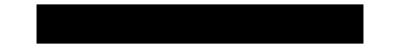
-Graphics-
In one-dimensional linear motion, say, a ball of mass m thrown upwards near the surface of the earth.  There are two state variables, the position s and momentum p of the ball.  The acceleration s̈ is assumed to be constant -g.  The pair of variables (s,p) completely determine a state of the system.  The equations that relate the quantities are

m ṡ=p
ṗ=-m g

-Graphics-
If different times are considered different states, even with the same position and velocity, then one might extend the pair to a triple (t,s,p).

-Graphics-
If the massive particle is thrown far away from the earth, then the gravity cannot be assumed to be constant but varies inversely as the square of the distance from the center of mass of the earth.  In this case it would be convenient to let the position be the distance from the center of mass.  The pair (s, p) still completely determine a state of the system, but the equations of the system become

m ṡ=p
ṗ=(-m g R^2)/s^2

where R is the radius of the earth.

-Graphics-
If we allow three-dimensional motion, then the position and momentum each need three numbers to specify them.  So a state of the system is completely determined by six real variables.  The equations of motion might still be represented

m ṡ=p
ṗ=-m g

We also might adopt a three-dimensional cartesian coordinate system (x,y,z), so that the position would be represented by s=(x,y,z) and the momentum by p =m ṡ=(p_x,p_y,p_z)=(m ẋ,m ẏ,m ż).  The we can write the equations of motion as a system of six equations:

m ẋ=p_x | m ẏ=p_y | m ż=p_z
(ṗ)_x=(-m g R^2 x)/((x^2+y^2+z^2)^(3/2)) | (ṗ)_y=(-m g R^2 y)/((x^2+y^2+z^2)^(3/2)) | (ṗ)_z=(-m g R^2 z)/((x^2+y^2+z^2)^(3/2))

-Graphics-
If the particle’s mass is changing, as in the case of a rocket, then the mass becomes a state variable.  Also the time-derivative of the momentum changes, since m=m(t) is a function of time:

ṗ=d/dt(m ṡ)=ṡ d/dt m+m d/dt ṡ=ṡ ṁ+m s̈

Here seven variables are need to completely determine a state and an equation m=m(t) must be given for the mass.

#### Phase space

The phase space of a system consists of all its possible states.  In the case where all the variables are represented by real numbers, as is the case in differential equations, we say that the dimension of the phase space (or of the system) is the number of variables.

For a differential equation of the form x^(n)=f(x,ẋ,...,x^(n-1)), with no explicit dependence on t, phase space is the n-dimensional space with coordinates that represent the possible values for the n-tuple (x,ẋ,...,x^(n-1)).

Typical examples.

For a first-order equation of the form ẋ=f(x), the phase space is a line with coordinate x.  For a second-order equation ẍ=f(x,ẋ), the phase space is a plane with coordinates (x,ẋ).  For a system of two first-order equations of the form ẋ=f(x,y),ẏ=g(x,y), the phase space is a plane with coordinates (x,y).

#### Extended phase space

In differential equations, the term phase space normally used when the states depend on the dependent variable(s) and their derivatives, but not one the independent variable(s).  When the differential equation has an explicit dependence on the independent variable, then the states depend on it and it should be part of the phase space.  In such a case, we sometime emphasize the inclusion of the independent variable by the term extended phase space.  For a differential equation of the form x^(n)=f(t, x,ẋ,...,x^(n-1)), with an explicit dependence on t, extended phase space is the (n+1)-dimensional space with coordinates that represent the possible values for the (n+1)-tuple (t,x,ẋ,...,x^(n-1)).

Typical examples.

For a first-order equation of the form ẋ=f(t,x), the phase space is a plane with coordinates (t,x). For a second-order equation ẍ=f(x,ẋ), the phase space is a three-dimensional space with coordinates (t,x,ẋ).

#### More terms

Some terminology:

The order of a differential equation is the order of the highest-order derivative that appears in the differential equation.

If there is only one independent variable, then the derivatives are all ordinary derivatives and the differential equation is called an ordinary differential equation.  If a dependent variable is a function of more than one independent variable, then its derivatives are partial derivatives and the differential equation is called a partial differential equation.

If the sides of a differential equation, as functions of the dependent variables, are polynomials, then the degree of the polynomial is called the degree of the differential equation.  The coefficients of the dependent variables may be any kind of function of the independent variables.

The equation e^x(d^3 y)/(d x^3)+y dy/dx+x^4 y=cos(x) is a third-order, second-degree, ordinary differential equation.  (Second-degree because the middle term is a product of two degree-one terms.  The degree of x does not matter, nor do the transcendental functions of x.)

### Integral curves and solutions

#### Evolutionary processes

We will be interested in processes whose change from state to state is described by system of equations involving the derivatives of the state variables.  The simplest involve just the first derivatives and the equations are called first-order differential equations.  They have the form

ẋ=v(t, x)

where x represents a variable or variables that describes a state of the process.  Second-order differential equations contain second derivatives and so on.  When the system is free of the independent variable t, such as in

ẋ=v(x),

the system is said to be autonomous.

#### The Phase space of a differential equation

To take the simplest case, a single autonomous first-order differential equation

ẋ=v(x),

where v is a continuous function*, the phase space consists of a real number line representing the state x.  The differential equation defines a vector field on the phase space — that is, to each point x on the line, we assign a “velocity vector” v(x).  The sign of v(x) determines the direction of change of the state x, and the magnitude give the speed.

*Remark.  Throughout the course, we will assume that our objects (functions, mappings, etc.) are sufficiently smooth, that is, that their derivatives exist and are continuous to whatever order is needed, unless other stated.

-Graphics-

Consider the differential equation

ẋ(t)=x(t) (1-x(t)).

A plot of the phase space, a real number line for x, is below.

```mathematica
If[!MemberQ[$Path,NotebookDirectory[]],AppendTo[$Path, NotebookDirectory[]],$Path];
Needs["diffEqClass`"];
Row[{vectorPlot1D[x(1-x),{x,-0.5,1.5},ImageSize->{Automatic,150},ImagePadding->{{20,20},{5,5}}],
Pane[Style["Phase space with the direction of the vector field","Remark"],150]
}]//Deploy
```

-Graphics-Phase space with the direction of the vector field

Figure FigureNumbered.  Phase portrait showing equilibria and phase velocity vectors.

At the two points x=0,1, the velocity is zero.  If the system is ever in this state, it will never change.  A point at which the phase velocity is zero is called an equilibrium point of the system.  There is a difference between them.  The motion is away from x=0 and it is towards x=1.If it is possible  for any distance to find an open neighborhood of an isolated equilibrium point such that a trajectory that starts from any point within the neighborhood remains within the distance, the equilibrium is said to be stable; otherwise it is unstable.

-Graphics-

For an example in two dimensions, we first take a second-order equation:

x^(..)(t)+x(t)=0

The state variables are x,ẋ and the phase velocity is given by their derivatives (ẋ,x^(..))=(ẋ,-x) , where x^(..)=-x is obtained from the differential equation.  To draw a picture of the velocity field , we first pick unit of time Δt=1 . The velocity vector may be represented by a displacement in the plane given by

(Δx,Δ ẋ)=(ẋ Δt,x^(..) Δt) = (ẋ,-x)Δt .

So for instance at the point (x,ẋ)=(2,1) , we can represent the velocity (ẋ, x^(..))=(1,-2) by an arrow that starts at (2,1) and moves over one unit and down two units.  We can repeat this process for many points to achieve a good picture of the phase velocity field.  We can also use a different unit of time Δt to scale the vectors so that our arrows do not overlap each other.  Mathematica’s VectorPlot will do this automatically for us.

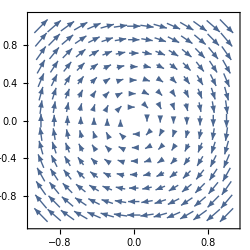

```mathematica
VectorPlot[{dx,-x},{x,-1,1},{dx,-1,1},ImageSize->250]
```

Figure FigureNumbered.  Two dimensional phase velocity field of a second-order differential equation.

Similarly, a system of two first-order differential equations has a two-dimensional phase space.  Consider

ẋ | = | x-2y
ẏ | = | 2x+y

The state variables are (x,y).  Below is a plot of its phase velocity field.

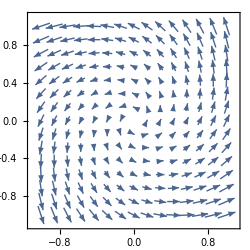

```mathematica
VectorPlot[{x-2y,2x+y},{x,-1,1},{y,-1,1},ImageSize->250]
```

Figure FigureNumbered.  Two dimensional phase velocity field of a system of two first-order differential equations.

In both cases, the origin (0,0) is an equilibrium point, which is easy to check.  It’s a little harder to tell that in second-order equation x^(..)(t)+x(t)=0 , it is stable, for the motion turns out to be clockwise rotation in which the trajectories are circles centered at the origin.  If we were to perturb the vectors in the field slightly, the trajectories might spiral in or spiral out.  In the (ẋ,ẏ) system, it’s a little easier to see from the larger vectors that the motion spirals out away from the origin, although it’s hard to see what happens close to the origin.  This equilibrium is unstable.

#### Integral curves

One way of looking at the equation

ẋ(t)=v(t,x)

is that at each point (t,x), the equation defines a slope ẋ or direction.  The assignment of a direction to each point in a region is called a direction field.

Now suppose a curve has the property that its tangent at each point has the same direction as the direction field.  Such a curve is called an integral curve.

Example

Here is a direction field on a plane that maps into itself when it is translated along a vertical line.

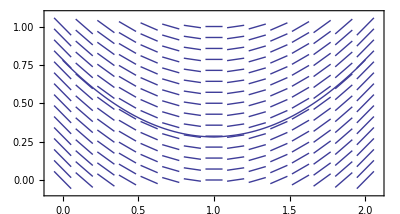

```mathematica
Show[
VectorPlot[{1,t-1},{t,0,2},{x,0,1},VectorStyle->{"Segment",Thin},AspectRatio->Automatic
],
StreamPlot[{1,t-1},{t,0,2},{x,0,1},AspectRatio->Automatic,StreamScale->Full,StreamPoints->{{1.,0.28}},StreamStyle->{Thick,Arrowheads[0]}
,
Frame->{{True,False},{True,False}}]
]//Deploy
```

Figure FigureNumbered.  An integral curve of field invariant with respect to vertical translations.

In such a field, the directions are independent of of x, so that v is just a function of t— that is, ẋ=v=v(t).  Finding the integral curves is the same as finding the integral of v: x=∫ v dt+C. Note that the integral curves are also mapped into themselves when translated vertically (represented by the +C).

#### Solutions of first-order equations

Corresponding to the geometric problem of finding an integral curve is the analytic solution of a differential equation.  A solution of a differential equation of the form

ẋ=v(t, x)

is a function f such that the substitution x=f(t), ẋ=f'(t) satisfies the equation.

If the equation is supplemented with an initial condition,

ẋ=v(t, x), x(t_0)=x_0,

the system is called an initial value problem (IVP).

ẋ=f'(t)=v(t,x)=v(t,f(t)).

Example

The solution to the initial value problem

ẋ=v(t), x(t_0)=x_0

is given by x(t)=x_0+∫_t_0^t v(t) dt.  We know from calculus that this solution is unique (since, if you recall, we are assuming v is continuous).

#### Numerical analysis

Direction Fields

We can write the differential equation ẋ=v(t, x) in differential form, where we replace ẋ by dx/dt and separate the differential:

dx-v(t,x) dt = 0.

More generally a differential equation might appear in the form

(*)	M(x,y) dx+N(x,y) dy=0

and we might consider either x or y the independent variable.  In either case, the coefficients M(x,y), N(x,y) determine a slope dy/dx at each point (x,y) where M,N are defined.

If a starting point (x_0,y_0) is chosen, then a line may be drawn with the slope determined by the differential equation (*).  The integral curve passing through the point will be tangent to the line.  Moving along the line a little way, we can choose a point that will approximate a point on the integral curve.  We can repeat this process from the new point to construct another point approximately on the integral curve.  In this way we accumulate points from which we can construct an approximation to the integral curve

An example with Mathematica code.

The equation we will examine is

dx-(x-t)dt=0, (t_0,x_0)=(0,0.5)

Solve  will return the solutions to an equation in the form of replacement rules (for example{t→0,x→0.5}).  Our ODE has only one solution for dx, which will be the first one.

```mathematica
First@Solve[
dx-(x-t)dt==0, (* solve ode for dx in terms of dt *)
dx]
```

{dx→-dt (t-x)}

One can plug in the replacement with the ReplaceAll operator /.:

```mathematica
{dt,dx}/.{dx->-dt (t-x)}
{dt,dx}/.{dx->-dt (t-x)}/.{t->0,x->0.5}/.dt->0.5
```

{dt,-dt (t-x)}

{0.5,0.25}

The commands Nest, NestList iterate a process (given by a function).  That means the output of the function is fed as input to the process repeatedly for a specified number of times.  NestList returns a list of all the values.  (It calculates f(f(...f(a)..)).)  The function in NestList below adds to the current value of {t,x} the changes {dt,dx} needed to get to the next step in the solution.

```mathematica
Clear[x,t,dx,dt]; (* clear any previous definitions *)
{t0,x0}={0,0.5};
ode =dx-(x-t)dt==0; 
Δt=0.5; (* step size *)
(* The #..& makes a function in which # represents the input argument *)
pts=NestList[
  (* a step to iterate *)
Function[{point},
point+{dt,dx}/. (* /.: plug in the following replacement for dx *)
First@Solve[
ode/. (* solve ode for dx in terms of dt *)
Thread[{t,x}->point],(* at the input point *)
dx]/.
dt->Δt (* plug in value of Δt for dt *)
],
  (* starting point of the process *)
{t0,x0},
3 (* number of iterations: 3 new points *)
]
```

{{0,0.5},{0.5,0.75},{1.,0.875},{1.5,0.8125}}

Map applies a function to all elements in a list.  Here we apply drawing commands for each point in pts that draw the tangent line indicated by the ODE and the point itself.

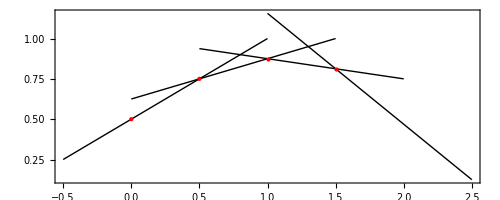

```mathematica
Graphics[{
Map[
  (* a function to apply to each point:
    # denotes the argument (= a point from pts) *)
With[{Δx=dx/. (* set Δx equal to the value of dx at the point *)
First@Solve[
ode/. (* solve ode for dx in terms of dt *)
Thread[{t,x}->#],(* at the input point *)
dx]/.dt->Δt},
{Thin,Line[{#-{Δt,Δx},#+2{Δt,Δx}}], (* draw a line *)
PointSize[Large],Red,Point[#]} (* draw a red point *)
]&,
pts]
},
Frame->True]
```

Exercise

Are the constructed points in the example above or below the actual integral curve that passes through the first point on the left?  Explain why.

#### Solutions of differential equations

To numerically  solve a differential equation comes down to solving a problem like this: To accurately estimate x at some time t_1 given a certain value of x at given initial time t_0.

The differential equation

ẋ=v(t, x)

specifies the rate of change of x at any given values of t,x.  And given the rate of change, we can estimate the change in x by multiplying by the change in t:

Δx=ẋ Δt=v(t,x)Δt

We can repeat this process as needed.

An example with Mathematica code.

The equation we will examine is

ẋ=(x-t), (t_0,x_0)=(0,0.5)

which is the same IVP as the preceding example, but in a different form.

```mathematica
Clear[x,t,v];
  (* N.B. v[x_,t_], v[{t_,x_}] are different formulas *)
v[{t_,x_}]:=x-t;
{t0,x0}={0,0.5};
Δt=0.5; (* step size *)
fnpts=NestList[
#+{Δt,v[#]Δt}&,
{t0,x0},
3
]
```

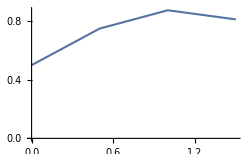

```mathematica
ListPlot[fnpts,
Joined->True,AxesOrigin->{0,0},ImageSize->250]
```

Exercise

Are the constructed values of x in the example greater or less the actual values of the solution to the IVP?  Explain why.  Relate to the exercise on integral curves in the previous example.

References to functions for iterative numerics

NestList[f,expr,n]

Nest[f,expr,n]

Map[f,expr]

Table[expr,{i,i_min,i_max}]

FixedPointList[f,expr]

FixedPoint[f,expr]

ListPlot[{{x_1,y_1},{x_2,y_2},…}]

ListLinePlot[{{x_1,y_1},{x_2,y_2},…}]

#### Phase portraits in Mathematica

There are various ways to visualize the differential equation

ẋ=v(x).

The function portrait1D is a function that is part of the package “diffEqClass`” for this course.  For example, consider this equation:

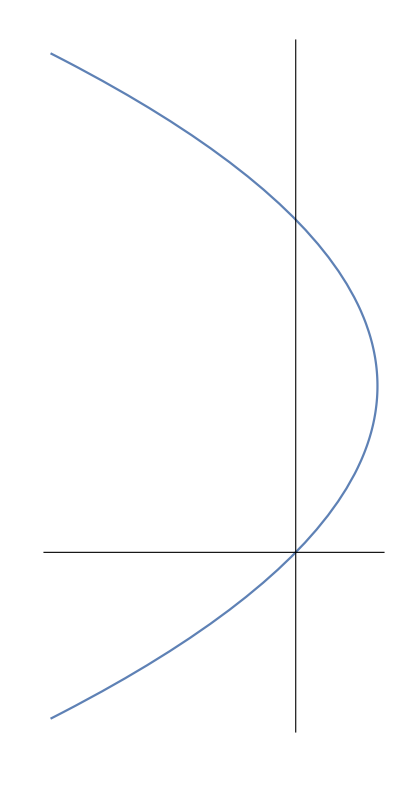
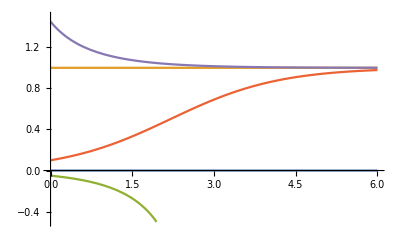
x'(t)==(1-x(t)) x(t) |  | 
-Graphics- | -Graphics- | -Graphics-
x vs. v | vector field | x vs. t

```mathematica
If[!MemberQ[$Path,NotebookDirectory[]],AppendTo[$Path, NotebookDirectory[]],$Path];
Needs["diffEqClass`"];
portrait1D[x'[t]==x[t](1-x[t]),{x[t],-0.5,1.5},{t,0,6}]//Deploy
```

Figure FigureNumbered.  The velocity graph, phase portrait, and integral curves of a first-order differential equation.

The figure shows three plots.  In each the vertical axis corresponds to x(t).  The left graph show the velocity v = x′(t).  The velocity is negative when the graph is to the left of the axis.  The middle graph indicates the orientation (up or down) of the velocity vectors.  The right graph show the plots of a few solutions

Click the button below to bring up an interactive example

```mathematica
Button[Style["interactive example","ExampleText"],
showExample[
"ODE Portrait",
"The phase phase and integral curves of an ode",
"Enter a first-order ode into the field.",
Manipulate[
portrait1D[ode/.p->p0,{x,-x1,x1},{t,0,t1}],
{{ode,x'[t]==p x[t]},InputField},
{{p0,0.1,"p"},0,1.0},
{{t1,2.,"t_f"},1.,10.},
{{x1,1.2,"range"},0.1,3.},
Initialization:>(
If[!MemberQ[$Path,NotebookDirectory[]],AppendTo[$Path, NotebookDirectory[]],$Path];
Needs["diffEqClass`"])],
{}
]
]
```

interactive example

-Graphics-

Visualizing a two-dimensional phase space or extended phase space may be done with StreamPlot or VectorPlot.  To do so, you need to form the expression for the corresponding vector field.

System of 1st-order

Differential Equation | Vector Field | Remarks
ẋ=v(t,x) | {1, v(t,x)} | Extended phase space
x^(..)=f(x,ẋ) | {ẋ,f(x,ẋ)} | 2nd-order DE phase space
{ẋ=u(x,y)
ẏ=v(x,y) | {u(x,y),v(x,y)} | System of 1st-order

Examples

Extended phase space: ẋ=(1-x)sin(t)

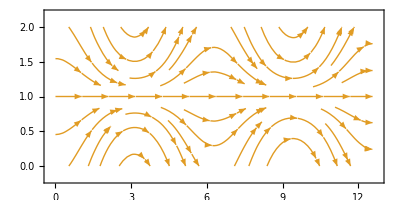

```mathematica
StreamPlot[{1,(1-x)Sin[t]}, (* vector field *)
{t,0,4Pi},{x,0,2}, (* domain *)
AspectRatio->Automatic,ImageSize->400]
```

Figure FigureNumbered.  Plot of the integral curves of a first-order equation.

The phase space of a second-order ordinary differential equation: x^(..)-2 ẋ+2x=0

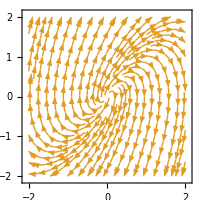

```mathematica
StreamPlot[{dx,2dx-2x},(* vector field *)
{x,-2,2},{dx,-2,2}, (* domain *)
AspectRatio->Automatic,ImageSize->200]
```

Figure FigureNumbered.  Plot of the phase space of a second-order equation..

The phase space of a system of two first-order ordinary differential equations:

ẋ=-x+3x y
ẏ=2y-3x y

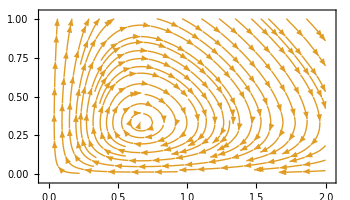

```mathematica
StreamPlot[
{-x+3x y,2y-3x y},(* vector field *)
{x,0,2},{y,0,1}, (* domain *)
AspectRatio->Automatic,ImageSize->350]
```

Figure FigureNumbered.  Plot of the phase space of a system of two first-order equations.

EquationTrekker

The EquationTrekker package, mentioned in 00 Introduction.nb and in the documentation center, can plot integral curves.

Execute the following (⇧-⌤) to bring up an interactive window.  Use the pen tool and click in the window to select an initial condition for (t,x).

```mathematica
Needs["EquationTrekker`"];
EquationTrekker[
x'[t]==x[t](1-x[t]),
x,
{t,0,6}]
```